```mathematica
Solve[{a+b+c+d==-2,8 a+4 b+2 c+d==-2,-27 a+9 b-3 c+d==0, 27 a-6 b+c==0}]
```

{{a→9/200,b→1/10,c→-123/200,d→-153/100}}

```mathematica
D[a x^3+b x^2+c x+d,x]==y/.{x->-3,y->0}
```

27 a-6 b+c==0

```mathematica
f[x_]:=a x^3+b x^2+c x+d/.{a->9/200,b->1/10,c->-123/200,d->-153/100}
```

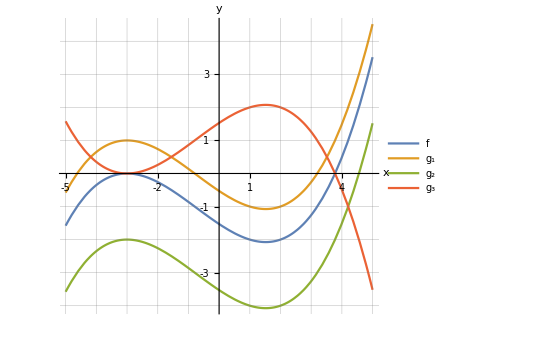

```mathematica
Plot[{f[x],f[x]+1,f[x]-2,-f[x]},{x,-5,5},AspectRatio->Automatic,PlotLegends->{f,Subscript[g,1],Subscript[g,2],Subscript[g,3]},GridLines->{Range[-5,5],Range[-5,5]},Ticks->{Range[-5,5],Range[-5,5]},AxesLabel->{x,y}]
```

```mathematica
NSolve[a x^3+b x^2+c x+d==-1/.{a->9/200,b->1/10,c->-123/200,d->-153/100},x]
```

{{x→-4.62612},{x→-0.795702},{x→3.1996}}

```mathematica
h=Interpolation[{{-5,0},{-3,2},{3,-2},{5,0}},InterpolationOrder->1]
```

InterpolatingFunction[…]

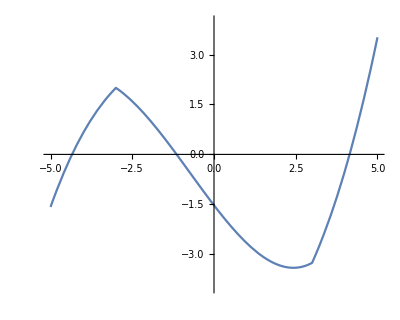

```mathematica
Plot[f[x]+h[x],{x,-5,5},PlotRange->{-4,4},AspectRatio->Automatic]
```

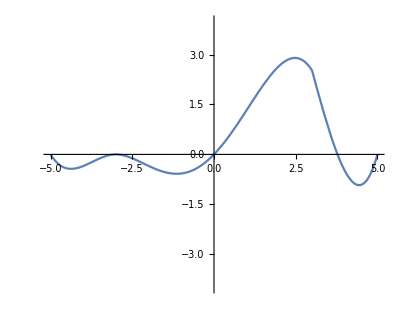

```mathematica
Plot[f[x]h[x],{x,-5,5},PlotRange->{-4,4},AspectRatio->Automatic]
```

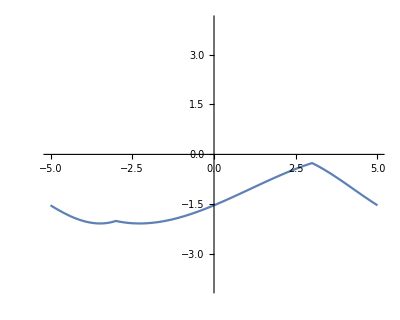

```mathematica
Plot[f[h[x]],{x,-5,5},PlotRange->{-4,4},AspectRatio->Automatic]
```

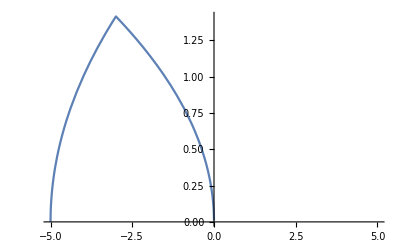

```mathematica
Plot[Sqrt[h[x]],{x,-5,5}]
```

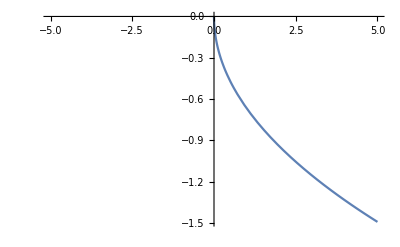

```mathematica
Plot[h[Sqrt[x]],{x,-5,5}]
```

```mathematica
Sqrt[729]
```

27

```mathematica
4+4 180
```

724

```mathematica
Solve[n/2 (n+2)==90]
```

{{n→-1-√181},{n→-1+√181}}

```mathematica
90 91/2
```

4095

```mathematica
25 13
```

325

```mathematica
Solve[4n^2+76n-2400==0]//N
```

{{n→-35.7726},{n→16.7726}}

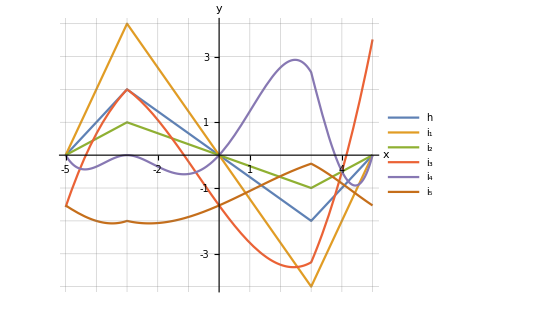

```mathematica
Plot[{h[x],2h[x],h[x]/2,h[x]+f[x],h[x]f[x],f[h[x]]},{x,-5,5},AspectRatio->Automatic,PlotLegends->Prepend[Subscript[i,#]&/@Range[5],HoldForm[h]],GridLines->{Range[-5,5],Range[-5,5]},AxesLabel->{x,y},Ticks->{Range[-5,5],Range[-5,5]}]
```